# Caminatas cuánticas

## Importando cosas

```mathematica
Get[NotebookDirectory[]<>"../AmadoTemp/DTQW.wl"]
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

## Definiendo variables

```mathematica
IndigoC=RGBColor["#729cfc"];
AquaC=RGBColor["#4bd7e5"];
DeepBlueC=RGBColor["#1e2c88"];
```

```mathematica
plotargs={
BaseStyle->{FontFamily->"LM Roman 12",FontSize->15},
PlotRange->All,
FrameLabel->(
Import[NotebookDirectory[]<>#,{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]]&/@{"Labels_pos.pdf","Labels_prob.pdf"}
),
Axes->False,
Frame->True,
Mesh->All,
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,Opacity[0.5]]
};
```

## Inicializaciones

```mathematica
InitializeDTQW[2,201]
MakeCoin[1/2,0,0];
MakeShift[];
MakeUnitary[];
```

```mathematica
plotlist={};
```

## Results

### Caminata clásica

```mathematica
probsC=Module[{n=100},
Riffle[Binomial[n,#]/2^n&/@Range[0,n],0]
];
```

```mathematica
Total@probsC
```

1

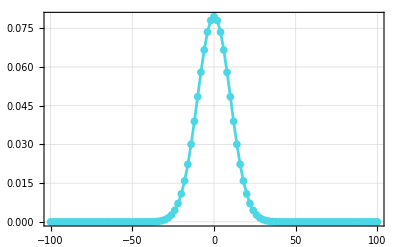

```mathematica
plotC=ListLinePlot[{Range[-100,100,2],probsC[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->AquaC
]
AppendTo[plotlist,ToString@Unevaluated@plotC];
```

### Caminatas cuánticas (sin decoherencia)

#### Estado inicial (+_y)_c⊗0_p

Empezar hablando de lo que son las caminatas cuánticas y mostrar un ejemplo de una caminata

```mathematica
psi0=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}]
```

VectorState[{{1/(√2),0,0},{ⅈ/(√2),1,0}}]

```mathematica
rhof0=#.#†&@DTQW2[psi0,100];
```

```mathematica
probs0=Abs@Diagonal@MatrixPartialTrace[rhof0,1,{2,201}];
```

```mathematica
Total@probs0
```

1.

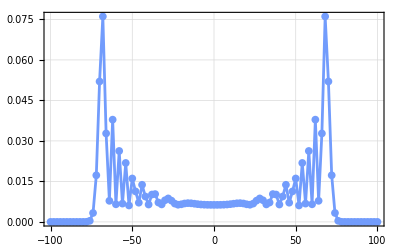

```mathematica
plot0=ListLinePlot[{Range[-100,100,2],probs0[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->IndigoC
]
AppendTo[plotlist,ToString@Unevaluated@plot0];
```

#### Estados iniciales 0⊗0 y 1⊗0

Las caminatas varían según condiciones iniciales de la moneda (idea de las condiciones)

```mathematica
psi1=VectorState[{{1,0,0}}];
psi2=VectorState[{{1,1,0}}];
```

```mathematica
rhof1=#.#†&@DTQW2[psi1,100];
rhof2=#.#†&@DTQW2[psi2,100];
```

```mathematica
probs1=Abs@Diagonal@MatrixPartialTrace[rhof1,1,{2,201}];
probs2=Abs@Diagonal@MatrixPartialTrace[rhof2,1,{2,201}];
```

```mathematica
Total/@{probs1,probs2}
```

{1.,1.}

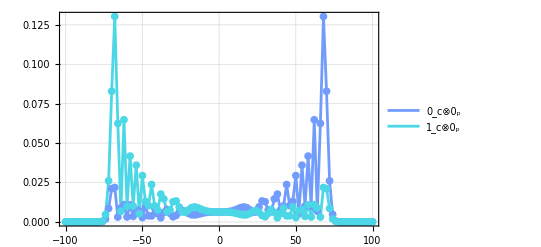

```mathematica
plot1y2=ListLinePlot[{
{Range[-100,100,2],probs1[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs2[[;;;;2]]}ᵀ
},
plotargs,
PlotStyle->{IndigoC,AquaC},
PlotLegends->{Subscript[Ket[{0}], c]⊗Subscript[Ket[{0}], p],Subscript[Ket[{1}], c]⊗Subscript[Ket[{0}], p]}
]
AppendTo[plotlist,ToString@Unevaluated@plot1y2];
```

#### Ejemplos más variados

```mathematica
psi3=VectorState[{{1/Sqrt[2],0,0},{1/Sqrt[2],1,0}}];
psi4=VectorState[{{1/Sqrt[2],0,20},{ⅈ/Sqrt[2],1,-20}}];
```

```mathematica
rhof3=#.#†&@DTQW2[psi3,100];
rhof4=#.#†&@DTQW2[psi4,100];
```

```mathematica
probs3=Abs@Diagonal@MatrixPartialTrace[rhof3,1,{2,201}];
probs4=Abs@Diagonal@MatrixPartialTrace[rhof4,1,{2,201}];
```

```mathematica
Total/@{probs3,probs4}
```

{1.,1.}

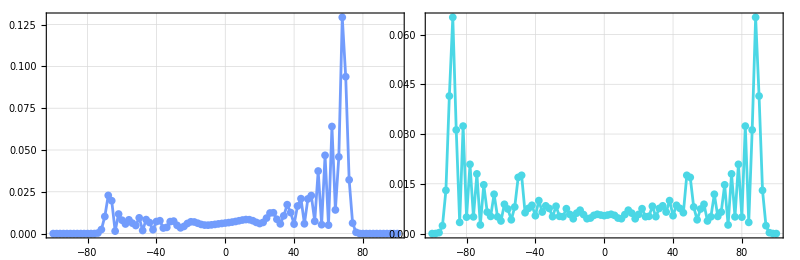

```mathematica
GraphicsGrid[{{
plot3=ListLinePlot[{Range[-100,100,2],probs3[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->IndigoC
],
plot4=ListLinePlot[{Range[-100,100,2],probs4[[;;;;2]]}ᵀ,
DeleteCases[plotargs,FrameLabel->_],
FrameLabel->{
Import["/home/amadoc/Desktop/Labels_pos.pdf",{"PDF","PageGraphics"},
ImageSize->{Automatic,16}
][[1]],
None
},
FrameTicksStyle->{Directive[Opacity->0,FontSize->0],None},
PlotStyle->AquaC
]
}},
Spacings->{Scaled[-0.15],0}
]
AppendTo[plotlist,ToString@Unevaluated@plot3];
AppendTo[plotlist,ToString@Unevaluated@plot4];
(* Poner lso labels o legends *)
```

### Caminatas con decoherencia

#### Introduciendo decoherencia

```mathematica
psi5=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhof5=DTQW2wDecoherence[psi0,0.99,100];
```

```mathematica
probs5=Abs@Diagonal@MatrixPartialTrace[rhof5,1,{2,201}];
```

```mathematica
Total[probs5]
```

1.

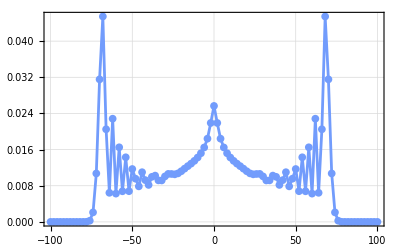

```mathematica
plot5=ListLinePlot[{Range[-100,100,2],probs5[[;;;;2]]}ᵀ,
plotargs,
PlotStyle->IndigoC
]
AppendTo[plotlist,ToString@Unevaluated@plot5];
```

#### Comparativa clásica vs cuántica vs cuántica w/decoherencia

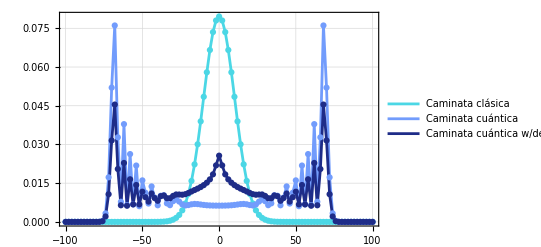

```mathematica
plotMix=ListLinePlot[{
{Range[-100,100,2],probsC[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs0[[;;;;2]]}ᵀ,
{Range[-100,100,2],probs5[[;;;;2]]}ᵀ
},
plotargs,
PlotStyle->{AquaC,IndigoC,DeepBlueC},
PlotLegends->{"Caminata clásica","Caminata cuántica","Caminata cuántica w/decoherecia"}
](* Mostrar en un label valor de  1-probabilidad *)
AppendTo[plotlist,ToString@Unevaluated@plotMix];
```

#### Gradiente variando p

```mathematica
psi6=VectorState[{{1/Sqrt[2],0,0},{ⅈ/Sqrt[2],1,0}}];
```

```mathematica
rhof6G=DTQW2wDecoherence[psi6,#,100]&/@(0.+Range[10]/1000);
```

```mathematica
probs6G=Abs@Diagonal@MatrixPartialTrace[#,1,{2,201}]&/@rhof6G;
```

```mathematica
Total/@probs6G
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

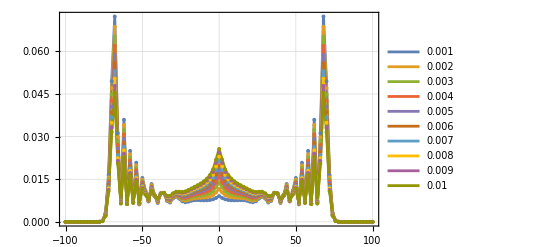

```mathematica
plot6=ListLinePlot[Evaluate@Table[{Range[-100,100,2],probs[[;;;;2]]}ᵀ,{probs,probs6G}],
plotargs,
PlotLegends->N[Range[10]/1000]
]
AppendTo[plotlist,ToString@Unevaluated@plot6];
```

#### Análogo clásico de estados iniciales de superposición

Propuesta de una caminata clásica con dos caminantes usando decoherencia

```mathematica
psi7=VectorState[{{1/Sqrt[2],0,20},{ⅈ/Sqrt[2],1,-20}}];
```

```mathematica
rhof7=DTQW2wDecoherence[psi7,0.5,100];
```

```mathematica
probs7=Abs@Diagonal@MatrixPartialTrace[rhof7,1,{2,201}];
```

```mathematica
Total@probs7
```

1.

Dos caminantes en una misma línea

```mathematica
probsC2=Module[{n=100},
p1=(ConstantArray[0,20]~Join~ Riffle[Binomial[n,#]&/@Range[0,n],0]/2^(n+1))[[;;201]];
p2=( Riffle[Binomial[n,#]&/@Range[0,n],0]~Join~ConstantArray[0,20]/2^(n+1))[[21;;]];
p1+p2
];
```

```mathematica
probsC2//Length
```

201

```mathematica
Total@probsC2//N
```

1.

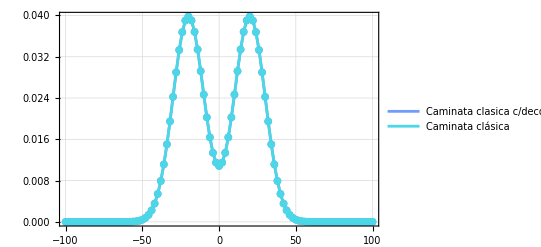

```mathematica
plot7yC2=ListLinePlot[{
{Range[-100,100,2],probs7[[;;;;2]]}ᵀ,
{Range[-100,100,2],probsC2[[;;;;2]]}ᵀ
},
plotargs,
PlotStyle->{IndigoC,AquaC},
PlotLegends->{"Caminata clasica c/decoherencia","Caminata clásica"}
]
AppendTo[plotlist,ToString@Unevaluated@plot7yC2];
```

### Caminatas de distintos operadores

Por hacer... (hay que arreglar el operador de shift)

## Exportando los resultados

```mathematica
Map[NotebookDirectory[]<>#<>".pdf"&,plotlist]
```

{/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/Mariana/plot0.pdf,/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/Mariana/plotC.pdf,/home/amadoc/Desktop/Programming/Mathematica/quantum_walks/Mariana/plot0.pdf}